```mathematica
data=SemanticImport["C:\\Users\\kylem\\Documents\\WSS-19 Homework Data\\UsageData_2019-06-01-00.00.00_23Days(1).csv"];
```

```mathematica
time=data[All,"IntervalEnd"]//Normal;
usage=data[All,"Quantity"]//Normal ;
morganincrementAT=AssociationThread[time->usage];
morganincrementTS=TimeSeries[morganincrementAT];
```

```mathematica
morganmaster=TimeSeriesInsert[morganmaster,morganincrementTS]
```

TimeSeries[…]

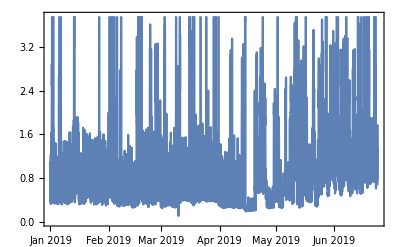

```mathematica
morganmasterHourlySum=TimeSeriesAggregate[morganmaster,"Hour",Total];
DateListPlot[morganmasterHourlySum]
```

```mathematica
morganmasterDailySum=TimeSeriesAggregate[morganmaster,"Day",Total];
```

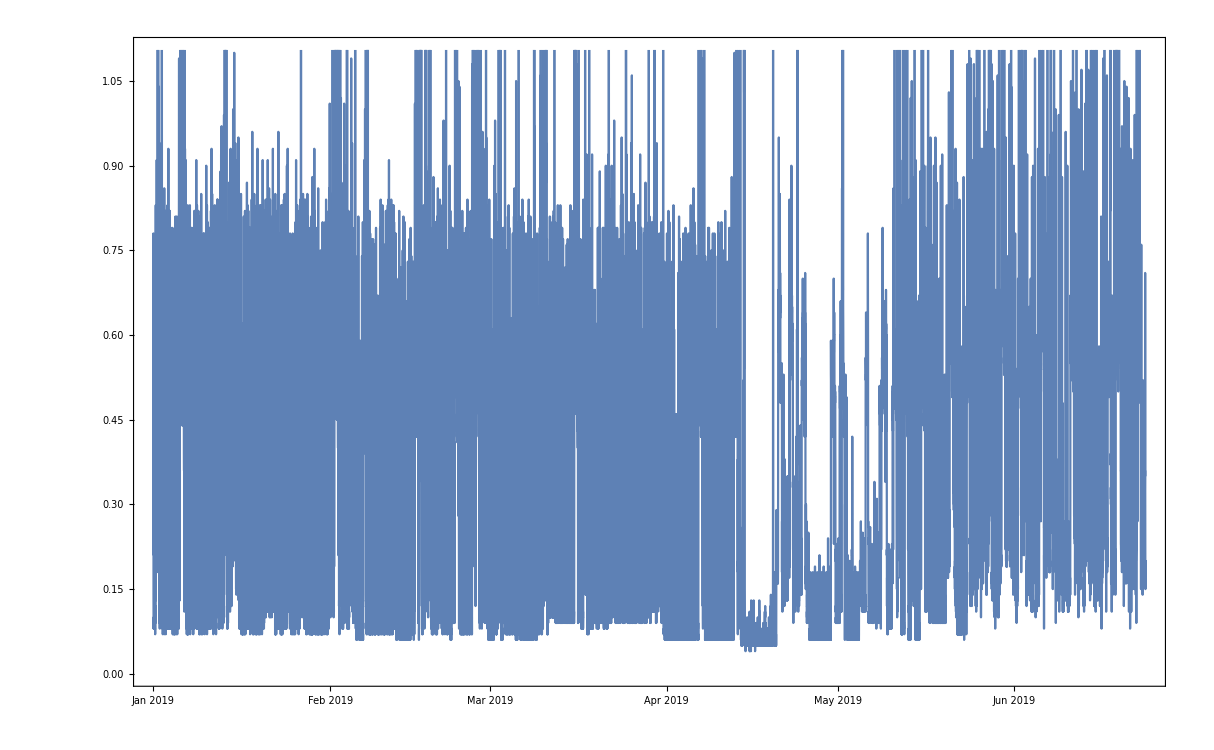

```mathematica
DateListPlot[morganmaster]
```

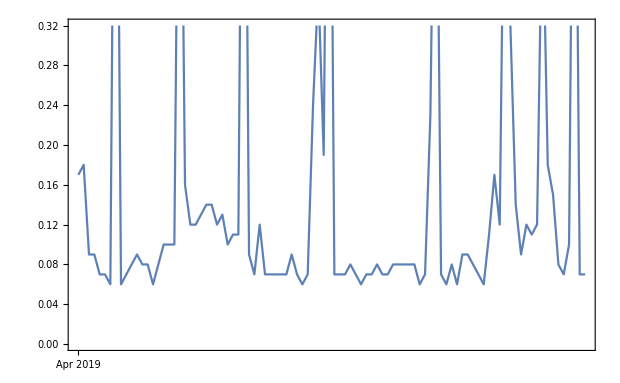

```mathematica
DateListPlot[TimeSeriesWindow[morganmaster,{{2019,4,1,0,0,0},{2019,4,1,23,59}}]]
```

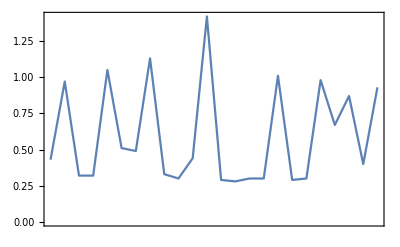

```mathematica
DateListPlot[TimeSeriesWindow[morganmasterHourlySum,{{2019,4,1,0,0,0},{2019,4,2,0,0}}]]
```

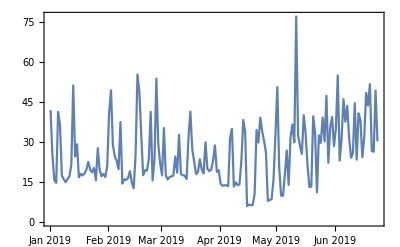

```mathematica
DateListPlot[morganmasterDailySum]
```

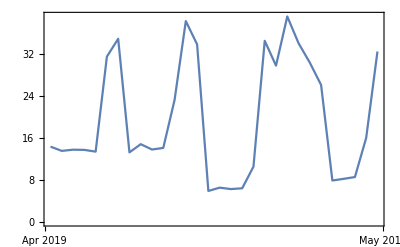

```mathematica
DateListPlot[TimeSeriesWindow[morganmasterDailySum,{{2019,4,1},{2019,5,1}}]]
```

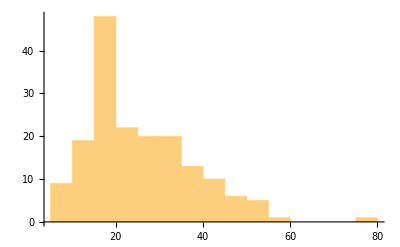

```mathematica
Histogram[morganmasterDailySum]
```

```mathematica
Mean[TimeSeriesWindow[morganmasterDailySum,{{2019,1,1},{2019,4,15}}]]
```

23.2264

```mathematica
Mean[TimeSeriesWindow[morganmasterDailySum,{{2019,4,16},{2019,5,11}}]]
```

21.75